Angle correlations were not utilized in first submission.

For figure 2, no separation between pnr and non-pnr region since they are all control videos

# Get single video info

```mathematica
video=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\no variation_model\\FullModel_param6_noVariation.tif"];
```

```mathematica
(*trim off border from model videos*)
video=ImagePad[#,-BorderDimensions@#]&/@video;
```

```mathematica
imageData=If[Length[ImageData[video[[1]]][[1,1]]]==3,Map[Mean,ImageData@#,{2}]&/@video,ImageData/@video];
```

```mathematica
dims=Reverse@Dimensions@First@imageData;
{xDim,yDim}=dims
```

{345,344}

```mathematica
Manipulate[
polyPs=Switch[pnr,"None",{},"Right",{pnrCntr,pnrTop,{xDim,yDim},{xDim,1},pnrBottom},"Left",{pnrCntr,pnrTop,{1,yDim},{1,1},pnrBottom}];

Show[
video[[frame]],
Graphics[
{
Red,PointSize@Medium,Point[centP],
Yellow,Opacity@.25,Polygon[polyPs]
}
]
],

{frame,1,Length@video,1},
{{pnr,"None"},{"Left","Right","None"}},
{{centP,IntegerPart/@{xDim/2,yDim/2}},Locator,Appearance->None},
{{pnrTop,{xDim/2,yDim}},{1,yDim},{xDim,yDim},Locator,Appearance->None},
{{pnrCntr,{xDim/2,yDim/2}},{1,1},{xDim,yDim},Locator,Appearance->None},
{{pnrBottom,{xDim/2,1}},{1,1},{xDim,1},Locator,Appearance->None},
Button["reset",centP=IntegerPart/@{xDim/2,yDim/2};rad=50;pnrTop={xDim/2,yDim};pnrBottom={xDim/2,1};pnr="None";pnrCntr={xDim/2,yDim/2};],
Button["save",
woundCenter=centP;
maxRads=yDim/2;
pnrPts=polyPs;
pnrSide=pnr;
startFrames=frame;]
]
```

Part::partd: Part specification video⟦21⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[video⟦21⟧,].

```mathematica
saveInfo={
"Model",
"C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\no variation_model\\FullModel_param6_noVariation.tif",
pnrPts,
pnrSide,
woundCenter,
maxRads,
startFrames};
```

```mathematica
Export["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\no variation_model\\info.m",saveInfo];
```

## Replace info into current infoAll from saved set (made in sections below)

```mathematica
infoAll=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\mathematica_RadialProfilePlot\\infoAll.m"];
```

```mathematica
Export["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\mathematica_RadialProfilePlot\\infoAll.m",Append[infoAll,saveInfo]];
```

# Get video set info (only need to do once per set of videos)

## Get File Names

```mathematica
fileNames=FileNames["*.tif","C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2",2][[{1,3,2}]]
```

{C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\control_Experiment\14April19_AG_R3_x_w1118_S5.tif,C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\noVariation\FullModel_param9_noVariation.tif,C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\control_Model\FullModel_param6_ControlVideo_GCaMP_PLC_Varied.tif}

```mathematica
{expFiles,modelFiles}=GatherBy[fileNames,StringContainsQ[#,__~~"Experiment"~~__]&]
```

{{C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\control_Experiment\14April19_AG_R3_x_w1118_S5.tif},{C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\noVariation\FullModel_param9_noVariation.tif,C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\control_Model\FullModel_param6_ControlVideo_GCaMP_PLC_Varied.tif}}

```mathematica
{expVideos,modelVideos}=Map[Import,{expFiles,modelFiles},{2}];

(*remove white border from model videos*)
modelVideos=Map[ImagePad[#,-BorderDimensions@#]&,modelVideos,{2}];
```

```mathematica
{imageDataExp,imageDataMod}=Map[ImageData,{expVideos,modelVideos},{3}];
```

```mathematica
{dimsExp,dimsMod}=Map[Reverse@Dimensions@First@#&,{imageDataExp,imageDataMod},{2}]//DeleteCases[#,3,{3}]&;
```

## Get video information by hand from experiment videos

Information needed
-- pnr region (technically the points that make up the polynomial)
-- side of pnr region (right vs left)
-- max radius (the farthest to go out to away from the wound
-- wound center
-- video dimensions
-- Start Frame

```mathematica
(*initialize lists*)
blankList=ConstantArray[0.,Length@expVideos];
{maxRadsExp,woundCenterExp,startFramesExp}=.;

(#=blankList)&/@{maxRadsExp,woundCenterExp,startFramesExp};
```

```mathematica
Manipulate[
{xDim,yDim}=dimsExp[[vid]];

Show[
expVideos[[vid,frame]],
Graphics[
{
Red,PointSize@Medium,Point[centP]
}
]
],

{vid,1,Length@expVideos,1},
{frame,1,Length@expVideos[[vid]],1},
{{centP,IntegerPart/@{xDim/2,yDim/2}},Locator,Appearance->None},
Button["save",
woundCenterExp[[vid]]=Round@centP;
maxRadsExp[[vid]]=Min[{#[[1]]-1,xDim-#[[1]],#[[2]]-1,yDim-#[[2]]}]&@centP;
startFramesExp[[vid]]=frame;]
]
```

```mathematica
(*For Model Videos*)
maxRadsMod=ConstantArray[Round[dimsMod[[1,2]]/2],Length@modelVideos];
woundCenterMod=ConstantArray[Round[dimsMod[[1]]/2],Length@modelVideos];
startFramesMod=ConstantArray[21,Length@modelVideos];
```

## Save Information

```mathematica
saveInfo=
Join[
Transpose@{ConstantArray["Experiment",Length@expVideos],expFiles,woundCenterExp,maxRadsExp,startFramesExp},
Transpose@{ConstantArray["Model",Length@modelVideos],modelFiles,woundCenterMod,maxRadsMod,startFramesMod}
];
```

```mathematica
Export["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\infoAll.m",saveInfo];
```

# Analysis

## Import videos, image data, and information from above

```mathematica
saveInfo=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\infoAll.m"];
```

```mathematica
videos=MapAt[Import,saveInfo,{All,2}][[;;,2]];

(*remove white border from model video frames*)
videos=Table[If[saveInfo[[vid,1]]=="Model",ImagePad[#,-BorderDimensions@#]&/@videos[[vid]],videos[[vid]]],{vid,Length@videos}];
```

```mathematica
types=saveInfo[[;;,1]];
imageData=Map[ImageData,videos,{2}];
dims=Map[Reverse@Dimensions@First@#&,imageData,{1}]//DeleteCases[#,3,{2}]&;
woundCenters=saveInfo[[;;,3]];
maxRads=Round@saveInfo[[;;,4]];
startFrames=saveInfo[[;;,5]];
```

## Get desired outputs

```mathematica
(*gets angle around the wound*)
getArcTan[{x_?NumberQ,y_?NumberQ},{wx_?NumberQ,wy_?NumberQ}]:=N@ArcTan[x-wx,y-wy]
```

```mathematica
(*Loop analysis across all videos*)
doCorr=False;

Monitor[
analysis=
Reap[
Do[
Block[
{video=videos[[vid]],type=types[[vid]],startFrame=startFrames[[vid]],center=woundCenters[[vid]],xDim=dims[[vid,1]],yDim=dims[[vid,2]],maxRad=maxRads[[vid]],

baseSubVideo,videoGauss,imageData,pixelsByRads,dataByRad,radProf,minPs,maxPs,half,r0s,interps,caRads,sDevProf,coeffVarProf,sortedByAngle,sortedByAngleShifted,thetaData,autoCorr},

(*Gaussian Blur and subtract image before wounding*)
videoGauss=GaussianFilter[#,2]&/@video;
baseSubVideo=(#-videoGauss[[startFrame-1]])&/@videoGauss;

(*account for RGB or grayscale*)
imageData=If[Length[ImageData[baseSubVideo[[1]]][[1,1]]]==3,Map[Mean,ImageData@#,{2}]&/@baseSubVideo,ImageData/@baseSubVideo];

(*separate pixels by radius. Convert from space cordinates to list indices*)
pixelsByRads=Reap[Table[Sow[{yDim-y+1,x},IntegerPart[Norm@{x-center[[1]],y-center[[2]]}]],{x,xDim},{y,yDim}],Range[0,maxRad]][[2,;;,1]];

(*Pull image data values based on radius and PNR side. Account for case of no points in pnr or non-pnr*)
dataByRad=Table[Extract[imageData[[im]],pixelsByRads[[rad]]],{im,Length@imageData},{rad,Length@pixelsByRads}];

(*Radial profile, only go up to maxRad*)
Sow[radProf=Map[Mean,dataByRad,{2}][[;;,;;maxRad]],"radProf"];

(*Adjust to pick correct time before wound and throw out nuclei image for data. Take 10th radius on to get rid of huge averages from smaller numbers of pixels*)minPs=(Mean@(#[[2,10;;]]))&@radProf;
maxPs=(Max@#[[10;;]])&/@#&@radProf;
half=(minPs+maxPs)/2;

(*find r0's to solve from*)
r0s=Flatten@Table[Ordering[radProf[[frame,10;;]]][[-1]]+9,{frame,Length@radProf}];

(*Use Interpolation functions to numerically solve with*)
interps=Map[Interpolation,radProf,{1}];

(*Find calcium radius vs time. Do not consider frames before wounding*)
Sow[caRads=Transpose@{2.14*(Range[Length@interps]-startFrame),Table[If[i<startFrame,0.,(r/If[type=="Model",yDim/450.,1.6])/.(FindRoot[interps[[i]][r]==half[[i]],{r,r0s[[i]],maxRad}])],{i,Length@interps}]},"caRads"];

Sow[ListLinePlot[#,
PlotRange->{{0,180},{0,150}},
PlotStyle->Black,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Ca^(2+) radius (μm)",None},{"time (s)",None}},
FrameStyle->Directive[Black,Bold,12],
FrameTicks->{{Range[0,150,30],None},{Range[0,180,30],None}},
AspectRatio->1

]&@caRads,"caRadPlots"];

Sow[sDevProf=Map[If[Length[#]≤1,0.,StandardDeviation@#]&,dataByRad,{2}][[;;,;;maxRad]],"sDevProf"];

Sow[coeffVarProf=sDevProf/radProf,"cvProf"];


(*(*BROKEN theta correlation BROKEN*)
sortedByAngle=Table[
If[Length@pixelsByRadsPNR[[ring]]<2,
pixelsByRadsPNR[[ring,1]],
SortBy[pixelsByRadsPNR[[ring,pnr]],getArcTan[#/.{row_?NumberQ,col_?NumberQ}->{col,yDim-row+1},center]&]],{ring,Length@pixelsByRadsPNR},{pnr,2}];

pnrIndex=If[pnrSide=="Left",1,2];

Sow[sortedByAngleShifted=Table[
If[Length@pixelsByRadsPNR[[ring]]<2,
pixelsByRadsPNR[[ring,1]],
ReplacePart[
sortedByAngle[[ring]],
pnrIndex->RotateLeft[sortedByAngle[[ring,pnrIndex]],Last@Ordering@Differences@Sort@(getArcTan[{#[[1]],#[[2]]},center]&/@(pixelsByRadsPNR[[ring,pnrIndex]]/.{row_?NumberQ,col_?NumberQ}->{col,yDim-row+1}))]]],{ring,Length@pixelsByRadsPNR}],"angleSort"];

If[doCorr,
thetaData=Table[Extract[imageData[[frame]],#]&/@sortedByAngleShifted[[rad]],{rad,Length@sortedByAngleShifted},{frame,Length@imageData}];
Sow[autoCorr=Table[CorrelationFunction[#,{0,Length[#]-1}]&/@thetaData[[rad,frame]],{rad,Length@sortedByAngleShifted},{frame,Length@imageData}],"autoCorr"];
Sow[autoCorr=Table[AbsoluteCorrelationFunction[#,{0,Length[#]-1}]&/@thetaData[[rad,frame]],{rad,Length@sortedByAngleShifted},{frame,Length@imageData}],"absAutoCorr"];];*)
],

{vid,Length@videos}]
,{"radProf","caRads","caRadPlots","sDevProf","cvProf","angleSort","autoCorr","absAutoCorr"}],

"Video "<>ToString[vid-1]<>" out of "<>ToString[Length@videos]<>" done."];
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[
{
Show[
videos[[vid,frame]],
Graphics[
{
Red,Circle[woundCenters[[vid]],analysis[[2,2,1,vid,frame,2]]*If[types[[vid]]=="Model",dims[[vid,2]]/450,1.6]]
}]
],

Show[analysis[[2,3,1,vid]],Graphics[{Green,Line[{{(frame-startFrames[[vid]])*2.14,0},{(frame-startFrames[[vid]])*2.14,200}}]}]](*,

ListLinePlot[analysis[[2,4,1,vid,frame]],PlotRange->{0,.25},PlotStyle->Black],

ListLinePlot[analysis[[2,5,1,vid,;;,frame]],PlotRange->{0,10.},PlotStyle->{Red,Black}]*)

},{vid,1,Length@videos,1},{frame,1,Length@videos[[vid]],1}]
```

# Figures

## Single Cell Plots

```mathematica
cellFilesExp=FileNames["*.csv","C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\singleCell\\Experiment"][[{1,3,2}]]
cellFilesModel=FileNames["*.csv","C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\singleCell\\Model"][[{1,3,2}]]
```

{C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\singleCell\Experiment\closeCell.csv,C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\singleCell\Experiment\middleCell.csv,C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\singleCell\Experiment\farCell.csv}

{C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\singleCell\Model\closeCell.csv,C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\singleCell\Model\middleCell.csv,C:\Users\Greg Stevens\Box\Research Backup\Current Work\NewCalciumModel\Full Model\Stevens et al\Figs\Fig2\singleCell\Model\farCell.csv}

```mathematica
{expData,modelData}=(Import/@#&/@{cellFilesExp,cellFilesModel})/.{t_?NumberQ,f_?NumberQ}->{(t-1)*2.14,f};
expData=expData[[;;,6;;]]/.{t_,f_}->{t-4*2.14,f};
modelData=modelData[[;;,21;;]]/.{t_,f_}->{t-19*2.14,f};
```

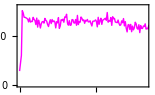
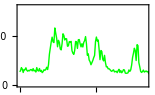
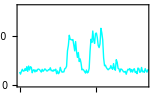
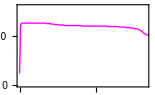
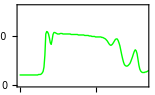
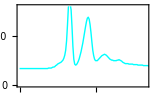

```mathematica
expList=Table[
ListLinePlot[{expData,modelData}[[i,j]],
PlotRange->{{0,300},{0,160}},
PlotStyle->Partition[Riffle[{Magenta,Green,Cyan},Thick,{2,-1,2}],2][[j]],
Axes->False,
Frame->{{True,False},{True,False}},
FrameTicks->{{Range[0,150,50],None},{Range[0,300,60],None}},
FrameStyle->Directive[Black,Bold,10,FontFamily->"Arial"],
FrameTicksStyle->Directive[Black,Bold,8,FontFamily->"Arial"],
ImageSize->{155,100}
]
,{i,2},{j,3}]
```

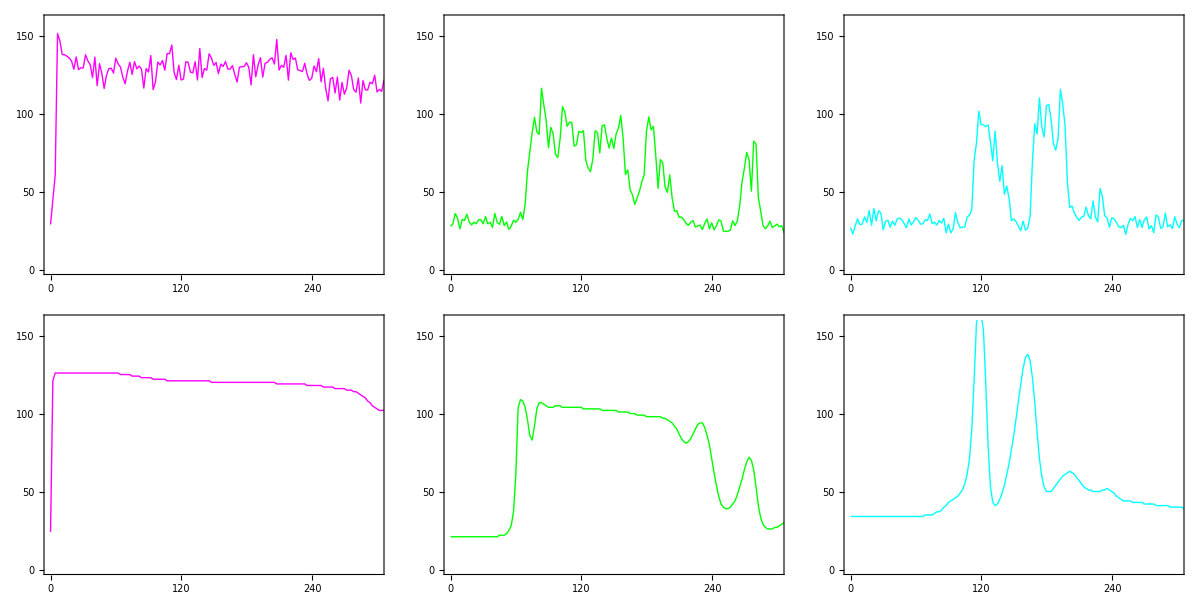

```mathematica
singleCellGrid=Grid[expList,Spacings->{.1,.1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["singleCellGrid.svg",singleCellGrid];
```

## Frames and Ca Rad Plots

```mathematica
caRads=analysis[[2,2,1]];

maxFirstExps=Table[Max[caRads[[vid,#;;#+Round[30/2.14],2]]]&@startFrames[[vid]],{vid,Length@videos}];

timeMaxFirstExps=Table[(First[Position[caRads,maxFirstExps[[vid]]]][[2]]-startFrames[[vid]])*2.14,{vid,Length@videos}]
```

{19.26,19.26,21.4}

```mathematica
micronExp=512/1.6;
micronModel=450;

newPixelModel=(micronExp)*dims[[2,2]]/micronModel;
```

```mathematica
SetDirectory[NotebookDirectory[]];

plotGrid=Grid[#,Spacings->{.1,.1}]&@
Table[
Join[
Show[
If[types[[vid]]=="Model",ImageCrop[#,{newPixelModel,newPixelModel}],#],
Graphics[
{Green,Dashed,Circle[If[types[[vid]]=="Model",{newPixelModel,newPixelModel}/2+{-1.5,-.5},woundCenters[[vid]]+{-5,-1}],If[types[[vid]]=="Experiment",1.6,dims[[vid,2]]/450]*maxFirstExps[[vid]]]}
]
,ImageSize->100]&/@videos[[vid,Table[startFrames[[vid]]+Round[t/2.14],{t,{0,timeMaxFirstExps[[vid]],80,145}}]]],

{ListLinePlot[#/.{t_,r_}/;t<0->Nothing,
PlotRange->{{0,200},{0,150}},
PlotStyle->Black,
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Ca^(2+) signal radius (μm)",None},{"time (s)",None}},
FrameTicksStyle->Directive[Black,Bold,6,FontFamily->"Arial"],
FrameStyle->Directive[Black,Bold,8,FontFamily->"Arial"],
FrameTicks->{{Range[0,150,30],None},{Range[0,200,50],None}},
AspectRatio->1.,
ImageSize->100

]&@caRads[[vid]]}

],
{vid,{1,2,3}}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
maxFirstExps
```

{58.7948,68.4114,65.4793}

```mathematica
Export["fig2FrameGrid.svg",plotGrid];
```

# Testing

## tangential autocorrelation

```mathematica
angleSorted=analysis[[2,6,1,2]];
```

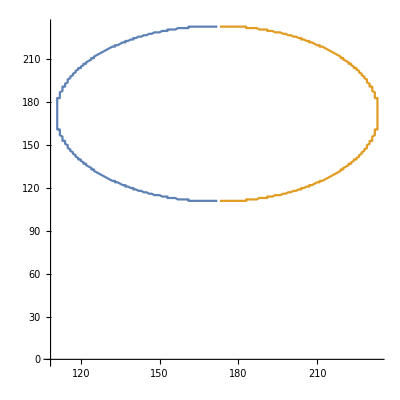

```mathematica
ListLinePlot[angleSorted[[62]]/.{row_?NumberQ,col_?NumberQ}->{col,dims[[11,2]]-row+1},AspectRatio->1]
```

```mathematica
videoGauss=GaussianFilter[#,2]&/@videos[[2]];
baseSubVideo=(#-videoGauss[[startFrames[[2]]-1]])&/@videoGauss;
```

```mathematica
testData=If[Length[ImageData[baseSubVideo[[1]]][[1,1]]]==3,Map[Mean,ImageData@#,{2}]&/@baseSubVideo,ImageData/@baseSubVideo];
```

```mathematica
Manipulate[
Block[{thetaData,autoCorr,absAutoCorr},

thetaData=Extract[testData[[frame]],#]&/@angleSorted[[rad]];
autoCorr=CorrelationFunction[#,{0,Length[#]-1}]&/@thetaData;
absAutoCorr=AbsoluteCorrelationFunction[#,{0,Length[#]-1}]&/@thetaData;

{
Show[baseSubVideo[[frame]],Graphics[{Red,Circle[woundCenters[[2]],rad]}]],

ListLinePlot[thetaData,ImageSize->Medium,PlotRange->All],

ListLinePlot[autoCorr,ImageSize->Medium,PlotRange->All],

ListLinePlot[absAutoCorr,ImageSize->Medium,PlotRange->All]
}],


{{frame,30},1,Length@baseSubVideo,1},
{{rad,10},1,Length@angleSorted,1}]
```

```mathematica
max2ndExpPix=170;
frame2ndExpStart=56;
frameFlaresEnd=114;
```

```mathematica
autoCorrs=Table[
Block[{thetaData,autoCorr},

thetaData=Extract[testData[[frame]],#]&/@angleSorted[[rad]];
CorrelationFunction[#,{0,Length[#]-1}]&/@thetaData
],
{rad,max2ndExpPix,Length@angleSorted,1},
{frame,frame2ndExpStart,frameFlaresEnd,1}];
```

```mathematica
Manipulate[ListLinePlot[{Mean@autoCorrs[[rad,;;,1]],Mean@autoCorrs[[rad,;;,2]]},PlotRange->{-.25,.25}],{rad,1,Length@autoCorrs,1}]
```

```mathematica
dims[[6]]
```

{345,344}

### collecting all at once from one video to put into the main loop

```mathematica
thetaData=Table[Extract[testData[[frame]],#]&/@angleSorted[[rad]],{rad,Length@angleSorted},{frame,Length@testData}];
autoCorr=Table[AbsoluteCorrelationFunction[#,{0,Length[#]-1}]&/@thetaData[[frame,rad]],{rad,Length@angleSorted},{frame,Length@testData}];
```

Extract::psl1: Position specification RotateLeft[{{173,172}},Last[{}]] in Extract[{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«295»},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«295»},«47»,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«295»},«294»},RotateLeft[«1»]] is not applicable.

General::stop: Further output of Extract::psl1 will be suppressed during this calculation.

```mathematica
thetaData//Dimensions
```

{173,207,2}

```mathematica
autoCorr=Table[AbsoluteCorrelationFunction[#,{0,Length[#]-1}]&/@thetaData[[frame,rad]],{rad,Length@angleSorted},{frame,Length@testData}];
```

Part::partw: Part 174 of {<<369104912 bytes>>} does not exist.

AbsoluteCorrelationFunction::invldd: The input data {<<369104912 bytes>>} should be a vector or a matrix of real numbers or a valid TemporalData object.

Part::pkspec1: The expression AbsoluteCorrelationFunction[174,{0,-1}] cannot be used as a part specification.

Part::partw: Part 175 of {<<369104912 bytes>>} does not exist.

AbsoluteCorrelationFunction::invldd: The input data {<<369104912 bytes>>} should be a vector or a matrix of real numbers or a valid TemporalData object.

Part::pkspec1: The expression AbsoluteCorrelationFunction[175,{0,-1}] cannot be used as a part specification.

Part::partw: Part 176 of {<<369104912 bytes>>} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

AbsoluteCorrelationFunction::invldd: The input data {<<369104912 bytes>>} should be a vector or a matrix of real numbers or a valid TemporalData object.

General::stop: Further output of AbsoluteCorrelationFunction::invldd will be suppressed during this calculation.

Part::pkspec1: The expression AbsoluteCorrelationFunction[176,{0,-1}] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

## FINSHED: Sorting ring pixels by angle around the wound (hodgepodge of stuff; cannot run without editing cells accordingly based on what is run in main notebook)

```mathematica
(*parts for list are: reap part 2, points by Rad part, something?, video, radius, pnr/non-pnr*)
Manipulate[ListPlot[test[[rad]]/.{row_?NumberQ,col_?NumberQ}->{col,dims[[6,2]]-row+1},PlotRange->{{1,dims[[6,1]]},{1,dims[[6,2]]}},AspectRatio->1,Epilog->{Yellow,Opacity@.25,Polygon@pnrPoints[[6]]}],{rad,1,Length@test,1}]
```

```mathematica
getArcTan[{x_?NumberQ,y_?NumberQ},{wx_?NumberQ,wy_?NumberQ}]:=N@ArcTan[x-wx,y-wy]
```

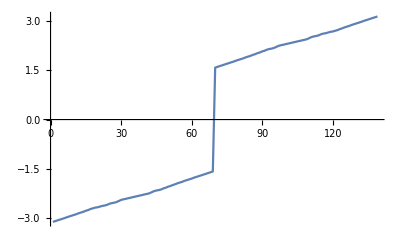

```mathematica
ListLinePlot@Sort@Map[getArcTan[{#[[1]],#[[2]]},woundCenters[[6]]]&,test[[43,1]]/.{row_?NumberQ,col_?NumberQ}->{col,dims[[6,2]]-row+1},{1}]
```

```mathematica
testSorted=Table[SortBy[test[[43,pnr]],getArcTan[#/.{row_?NumberQ,col_?NumberQ}->{col,dims[[6,2]]-row+1},woundCenters[[6]]]&],{pnr,2}];
correctSorted=ReplacePart[testSorted,1->RotateLeft[testSorted[[1]],Last@Ordering@Differences@Sort@(getArcTan[{#[[1]],#[[2]]},woundCenters[[6]]]&/@(test[[43,1]]/.{row_?NumberQ,col_?NumberQ}->{col,dims[[6,2]]-row+1}))]];
```

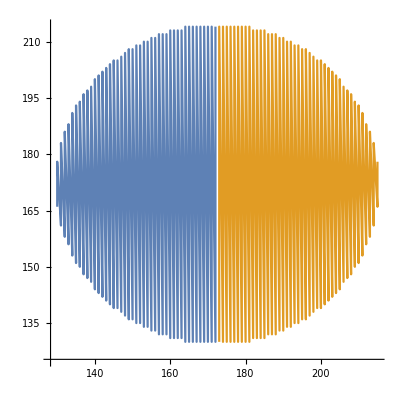

```mathematica
ListLinePlot[#,AspectRatio->1]&@({test[[43,1]],test[[43,2]]}/.{row_?NumberQ,col_?NumberQ}->{col,dims[[6,2]]-row+1})
```

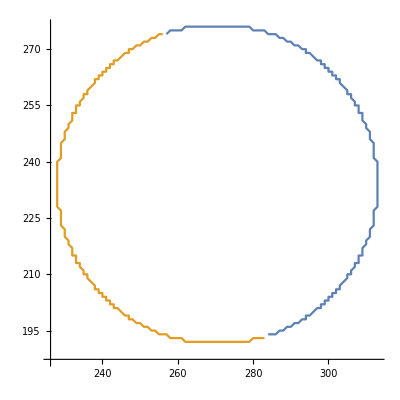

```mathematica
ListLinePlot[#/.{row_?NumberQ,col_?NumberQ}->{col,dims[[6,2]]-row+1},AspectRatio->1]&@ReplacePart[testSorted,2->RotateLeft[testSorted[[2]],82]]
```

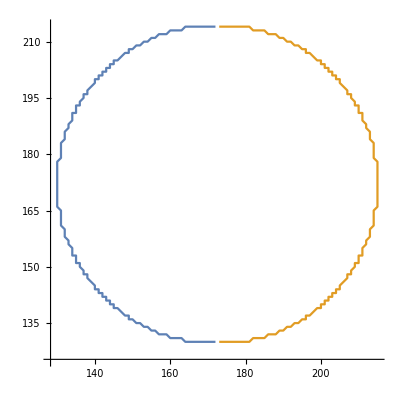

```mathematica
ListLinePlot[correctSorted/.{row_?NumberQ,col_?NumberQ}->{col,dims[[6,2]]-row+1},AspectRatio->1]
```

### gotta find the largest jump in differences

```mathematica
sortedAngles=Sort@Map[getArcTan[{#[[1]],#[[2]]},woundCenters[[1]]]&,analysis[[2,1,1,1,43,2]]/.{row_?NumberQ,col_?NumberQ}->{col,512-row+1},{1}];
```

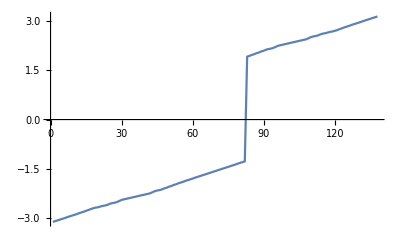

```mathematica
ListLinePlot@sortedAngles
```

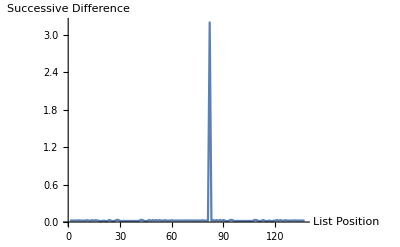

```mathematica
ListLinePlot[Differences@sortedAngles,PlotRange->All,AxesLabel->{"List Position","Successive Difference"}]
```

```mathematica
Last@Ordering@Differences@sortedAngles
```

82

```mathematica
(Differences@sortedAngles)[[82]]
```

3.19343

differences[[82]] means difference between point 83 and 82, so the jump happens from point 82 to point 83. This means we want to shift the points so that 83 is the first point

```mathematica
Length@sortedAngles
```

138

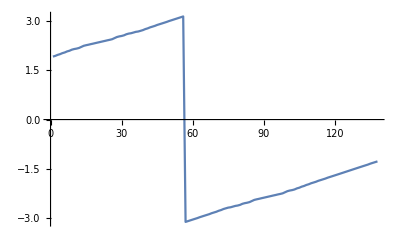

```mathematica
ListLinePlot@RotateLeft[sortedAngles,82]
```

### Apply to all rings of one video

```mathematica
getArcTan[{x_?NumberQ,y_?NumberQ},{wx_?NumberQ,wy_?NumberQ}]:=N@ArcTan[x-wx,y-wy]
```

```mathematica
testSorted=Table[
If[Length@analysis[[2,1,1,1,ring]]<2,
analysis[[2,1,1,1,ring,1]],
SortBy[analysis[[2,1,1,1,ring,pnr]],getArcTan[#/.{row_?NumberQ,col_?NumberQ}->{col,512-row+1},woundCenters[[1]]]&]],{ring,Length@analysis[[2,1,1,1]]},{pnr,2}];

correctSorted=Table[
If[Length@analysis[[2,1,1,1,ring]]<2,
analysis[[2,1,1,1,ring,1]],
ReplacePart[
testSorted[[ring]],
2->RotateLeft[testSorted[[ring,2]],Last@Ordering@Differences@Sort@(getArcTan[{#[[1]],#[[2]]},woundCenters[[1]]]&/@(analysis[[2,1,1,1,ring,2]]/.{row_?NumberQ,col_?NumberQ}->{col,512-row+1}))]]],{ring,Length@analysis[[2,1,1,1]]}];
```

```mathematica
Manipulate[ListLinePlot[correctSorted[[ring]]/.{row_?NumberQ,col_?NumberQ}->{col,512-row+1},AspectRatio->1,PlotRange->{{1,512},{1,512}}],{ring,1,Length@testSorted,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["angleSort.avi",Table[ListLinePlot[correctSorted[[ring]]/.{row_?NumberQ,col_?NumberQ}->{col,512-row+1},AspectRatio->1,PlotRange->{{1,512},{1,512}}],{ring,1,Length@testSorted,1}],"FrameRate"->100];
```

```mathematica
Length@testSorted
```

275

# Old Stuff

## Correlation testing

```mathematica
corrs=analysis[[2,{7,8},1]];
```

```mathematica
Manipulate[
{
Show[videos[[video,frame]],Graphics[{Red,Circle[woundCenters[[video]],rad],Yellow,Opacity@.25,Polygon@pnrPoints[[video]]}]],
ListLinePlot[corrs[[1,video,rad,frame]],ImageSize->Medium,PlotRange->All],
ListLinePlot[corrs[[2,video,rad,frame]],ImageSize->Medium,PlotRange->All]
},

{video,1,Length@videos,1},
{{frame,20},1,Length@videos[[video]],1},
{{rad,50},1,Length@corrs[[1,video]],1}]
```

## From Scratch

```mathematica
video=videos[[3]];
```

```mathematica
imageData=If[Length[ImageData[video[[1]]][[1,1]]]==3,Map[Mean,ImageData@#,{2}]&/@video,ImageData/@video];
```

```mathematica
{xDim,yDim}={Length@#[[1]],Length@#}&@(imageData[[1]])
```

{512,512}

```mathematica
pixelsPerMicron=1.6; (*1.6 for data, yDim/450 for model*)
```

```mathematica
Manipulate[
polyPs=Switch[pnr,"None",{},"Right",{pnrCntr,pnrTop,{xDim,yDim},{xDim,1},pnrBottom},"Left",{pnrCntr,pnrTop,{1,yDim},{1,1},pnrBottom}];

Show[
video[[frame]],
Graphics[
{
Red,PointSize@Medium,Point[centP],
Green,Circle[centP,rad],
Yellow,Opacity@.25,Polygon[polyPs]
}
]
],

{frame,1,Length@video,1},
{{rad,50},1,xDim,1},
{{pnr,"None"},{"None","Right","Left"}},
{{centP,IntegerPart/@{xDim/2,yDim/2}},Locator,Appearance->None},
{{pnrTop,{xDim/2,yDim}},{1,yDim},{xDim,yDim},Locator,Appearance->None},
{{pnrCntr,{xDim/2,yDim/2}},{1,1},{xDim,yDim},Locator,Appearance->None},
{{pnrBottom,{xDim/2,1}},{1,1},{xDim,1},Locator,Appearance->None},
Button["reset",centP=IntegerPart/@{xDim/2,yDim/2};rad=50;pnrTop={xDim/2,yDim};pnrBottom={xDim/2,1};pnr="None"],
Button["save",center=centP;maxRad=rad;pnrRegion=Region@Polygon@If[polyPs=={},{{1,1},{1,yDim},{xDim,yDim},{xDim,1}},polyPs];pnrSide=pnr]
]
```

```mathematica
startFrame=13;
```

```mathematica
videoGauss=GaussianFilter[#,2]&/@video;
```

```mathematica
(*baseSubVideo=(#-videoGauss[[startFrame-1]])&/@videoGauss;*)
baseSubVideo=video;

imageData=If[Length[ImageData[baseSubVideo[[1]]][[1,1]]]==3,Map[Mean,ImageData@#,{2}]&/@baseSubVideo,ImageData/@baseSubVideo];
```

```mathematica
Monitor[pixelsByRads=Reap[Table[Sow[{yDim-y+1,x},IntegerPart[Norm@{x-center[[1]],y-center[[2]]}]],{x,xDim},{y,yDim}],Range[0,maxRad]][[2,;;,1]];,Round[N[{x/xDim,y/yDim}*100],.1]]
```

```mathematica
(*Custom function to check if in pnr Region using fact that we have linear boundaries. Much fast than RegionMember function*)
checkPNR[coord_,pps_,pnrSide_]:=
Block[{x=coord[[1]],y=coord[[2]],xc=pps[[1,1]],yc=pps[[1,2]],xT=pps[[2,1]],yT=pps[[2,2]],xB=pps[[-1,1]],yB=pps[[-1,2]],slopeT,slopeB},
slopeT=(yT-yc)/(xT-xc);
slopeB=(yB-yc)/(xB-xc);

Which[
y==yc,If[pnrSide=="Right",x≥xc,x≤xc],
y>yc&&pnrSide=="Right",If[slopeT<0,y≥slopeT*x+(yc-slopeT*xc),y≤slopeT*x+(yc-slopeT*xc)],
y<yc&&pnrSide=="Right",If[slopeB>0,y≤slopeB*x+(yc-slopeB*xc),y≥slopeB*x+(yc-slopeB*xc)],
y>yc&&pnrSide=="Left",If[slopeT<0,y≤slopeT*x+(yc-slopeT*xc),y≥slopeT*x+(yc-slopeT*xc)],
y<yc&&pnrSide=="Left",If[slopeB>0,y≥slopeB*x+(yc-slopeB*xc),y≤slopeB*x+(yc-slopeB*xc)]
]
]
```

```mathematica
(*gather by PNR and non-PNR*)
isModel=False;
pixelsByRadsPNR=GatherBy[#,If[isModel,#[[2]]<xDim/2,checkPNR[#/.{row_,col_}->{col,yDim-row+1},polyPs,pnrSide]]&]&/@pixelsByRads;
```

```mathematica
(*(*gather by PNR and non-PNR*)
isModel=False;
pixelsByRadsPNR=GatherBy[#,If[isModel,#[[2]]<xDim/2,RegionMember[pnrRegion,#/.{row_,col_}->{col,yDim-row+1}]]&]&/@pixelsByRads;*)
```

```mathematica
(*Make sure PNR always comes first*)
pixelsByRadsPNR=Table[If[Length[#[[i]]]>1&&RegionMember[pnrRegion,#[[i,1,1]]/.{row_,col_}->{col,yDim-row+1}],#[[i]],Reverse@(#[[i]])],{i,Length@#}]&@pixelsByRadsPNR;
```

```mathematica
(*Monitor[dataByRad=Table[Extract[imageData[[im]],pixelsByRads[[rad]]],{im,Length@imageData},{rad,Length@pixelsByRads}];,Round[{im/Length@imageData,rad/Length@pixelsByRads}*100,.1]]*)
```

```mathematica
Monitor[dataByRad=Table[Extract[imageData[[im]],If[Length@pixelsByRadsPNR[[rad]]>1,pixelsByRadsPNR[[rad,pnr]],pixelsByRadsPNR[[rad,1]]]],{pnr,{1,2}},{im,Length@imageData},{rad,Length@pixelsByRadsPNR}];,Join[{pnr},Round[{im/Length@imageData,rad/Length@pixelsByRadsPNR}*100,.1]]]
```

```mathematica
radProf=Map[Mean,dataByRad,{3}][[;;,;;,;;maxRad]];
```

```mathematica
(*Adjust to pick correct time before wound and throw out nuclei image for data. Take 5th radius on to get rid of huge averages from smaller numbers of pixels*)
minPs=(Mean@(#[[2,10;;]]))&/@radProf;
maxPs=(Max@#[[10;;]])&/@#&/@radProf;
half=(minPs+maxPs)/2;
```

```mathematica
(*find r0's to solve from*)
r0s=Flatten/@Table[Ordering[radProf[[pnr,frame,10;;]]][[-1]]+9,{pnr,{1,2}},{frame,Length@radProf[[pnr]]}];
```

```mathematica
Manipulate[

ListLinePlot[radProf[[;;,i]],PlotRange->{0,150/255},Epilog->{{Blue,Line@{{r0s[[1,i]],0},{r0s[[1,i]],200}},Blue,Line@{{0,half[[1,i]]},{300,half[[1,i]]}}},{{Orange,Line@{{r0s[[2,i]],0},{r0s[[2,i]],200}}},Orange,Line@{{0,half[[2,i]]},{300,half[[2,i]]}}}}],{i,1,Length@radProf[[1]],1}]
```

```mathematica
interps=Map[Interpolation,radProf,{2}];
```

```mathematica
caRads=Table[Transpose@{2.14*(Range[Length@interps[[pnr]]]-startFrame),Table[If[i<startFrame,0.,r/pixelsPerMicron/.(FindRoot[interps[[pnr,i]][r]==half[[pnr,i]],{r,r0s[[pnr,i]],maxRad}])],{i,Length@interps[[pnr]]}]},{pnr,{1,2}}];
```

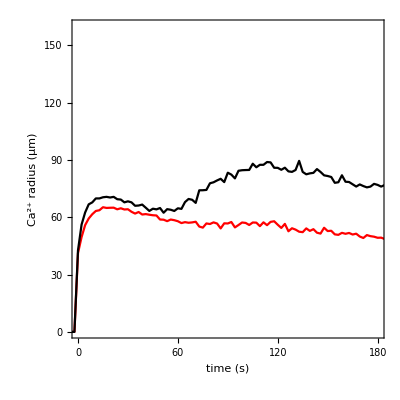

```mathematica
plot=ListLinePlot[#,
PlotRange->{{0,180},{0,160}},
PlotStyle->{Red,Black},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Ca^(2+) radius (μm)",None},{"time (s)",None}},
FrameStyle->Directive[Black,Bold,20],
FrameTicks->{{Range[0,150,30],None},{Range[0,180,30],None}},
AspectRatio->1

]&@caRads
```

```mathematica
Manipulate[Show[baseSubVideo[[i]],Graphics[{Blue,Circle[center,caRads[[1,i,2]]*pixelsPerMicron],Red,Circle[center,caRads[[2,i,2]]*pixelsPerMicron],Yellow,Opacity@.25,Polygon@polyPs}]],{i,1,Length@baseSubVideo,1}]
```

```mathematica
rad1exp=Max[Max[#[[startFrame;;Round[startFrame+30/2.14,2]]]]&/@caRads]
```

56.9573

```mathematica
(*frames*)
frames=Show[video[[#]],Graphics[{Yellow,Line[{#[[2]],#[[1]],#[[-1]]}]&@polyPs,Green,Dashed,Circle[center,rad1exp*pixelsPerMicron]}]]&/@{startFrame,Round[15/2.14]+startFrame,Round[120/2.14]+startFrame}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
info={"GJKdn_Experiment\\4-28-17_Inx2RNAi29306-ActinGCaMP6m_pupa2.tif",

{center,maxRad,pnrRegion,polyPs},

pixelsByRadsPNR,

radProf,

caRads,

plot,

frames
};
```

```mathematica
Export["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\GJKdn_Experiment\\info.m",info];
```

## From previously saved run

```mathematica
video=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\GJKdn_Experiment\\4-28-17_Inx2RNAi29306-ActinGCaMP6m_pupa2.tif"];
```

```mathematica
info=Import["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\GJKdn_Experiment\\info.m"];
```

```mathematica
imageData=If[Length[ImageData[video[[1]]][[1,1]]]==3,Map[Mean,ImageData@#,{2}]&/@video,ImageData/@video];
```

```mathematica
{xDim,yDim}={Length@#[[1]],Length@#}&@(imageData[[1]])
```

{512,512}

```mathematica
pixelsPerMicron=1.6; (*1.6 for data, yDim/450 for model*)
```

```mathematica
Manipulate[
polyPs=Switch[pnr,"None",{},"Right",{pnrCntr,pnrTop,{xDim,yDim},{xDim,1},pnrBottom},"Left",{pnrCntr,pnrTop,{1,yDim},{1,1},pnrBottom}];

Show[
video[[frame]],
Graphics[
{
Red,PointSize@Medium,Point[centP],
Green,Circle[centP,rad],
Yellow,Opacity@.25,Polygon[polyPs]
}
]
],

{frame,1,Length@video,1},
{{rad,info[[2,2]]},1,xDim,1},
{{pnr,"Left"},{"None","Right","Left"}},
{{centP,info[[2,1]]},Locator,Appearance->None},
{{pnrTop,info[[2,4,2]]},{1,yDim},{xDim,yDim},Locator,Appearance->None},
{{pnrCntr,info[[2,4,1]]},{1,1},{xDim,yDim},Locator,Appearance->None},
{{pnrBottom,info[[2,4,5]]},{1,1},{xDim,1},Locator,Appearance->None},
Button["reset",centP=IntegerPart/@{xDim/2,yDim/2};rad=50;pnrTop={xDim/2,yDim};pnrBottom={xDim/2,1};pnr="None"],
Button["save",center=centP;maxRad=rad;pnrRegion=Region@Polygon@If[polyPs=={},{{1,1},{1,yDim},{xDim,yDim},{xDim,1}},polyPs]]
]
```

```mathematica
200*pixelsPerMicron
```

320.

```mathematica
startFrame=16;
```

```mathematica
pixelsByRadsPNR=info[[3]];
```

```mathematica
Monitor[dataByRad=Table[Extract[imageData[[im]],If[Length@pixelsByRadsPNR[[rad]]>1,pixelsByRadsPNR[[rad,pnr]],pixelsByRadsPNR[[rad,1]]]],{pnr,{1,2}},{im,Length@imageData},{rad,Length@pixelsByRadsPNR}];,Join[{pnr},Round[{im/Length@imageData,rad/Length@pixelsByRadsPNR}*100,.1]]]
```

```mathematica
radProf=Map[Mean,dataByRad,{3}][[;;,;;,;;maxRad]];
```

```mathematica
(*Adjust to pick correct time before wound and throw out nuclei image for data. Take 5th radius on to get rid of huge averages from smaller numbers of pixels*)
minPs=(Mean@(#[[2,10;;]]))&/@radProf;
maxPs=(Max@#[[10;;]])&/@#&/@radProf;
half=(minPs+maxPs)/2;
```

```mathematica
(*find r0's to solve from*)
r0s=Flatten/@Table[Ordering[radProf[[pnr,frame,10;;]]][[-1]]+9,{pnr,{1,2}},{frame,Length@radProf[[pnr]]}];
```

```mathematica
Manipulate[

ListLinePlot[radProf[[;;,i]],PlotRange->{0,150/255},Epilog->{{Blue,Line@{{r0s[[1,i]],0},{r0s[[1,i]],200}},Blue,Line@{{0,half[[1,i]]},{300,half[[1,i]]}}},{{Orange,Line@{{r0s[[2,i]],0},{r0s[[2,i]],200}}},Orange,Line@{{0,half[[2,i]]},{300,half[[2,i]]}}}}],{i,1,Length@radProf[[1]],1}]
```

```mathematica
interps=Map[Interpolation,radProf,{2}];
```

```mathematica
caRads=Table[Transpose@{2.14*(Range[Length@interps[[pnr]]]-startFrame),Table[If[i<startFrame,0.,r/pixelsPerMicron/.(FindRoot[interps[[pnr,i]][r]==half[[pnr,i]],{r,r0s[[pnr,i]],maxRad}])],{i,Length@interps[[pnr]]}]},{pnr,{1,2}}];
```

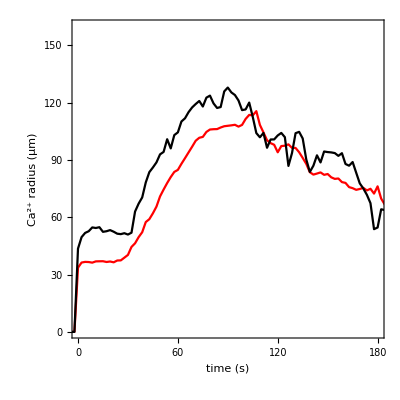

```mathematica
plot=ListLinePlot[#,
PlotRange->{{0,180},{0,160}},
PlotStyle->{Red,Black},
Axes->False,
Frame->{{True,False},{True,False}},
FrameLabel->{{"Ca^(2+) radius (μm)",None},{"time (s)",None}},
FrameStyle->Directive[Black,Bold,20],
FrameTicks->{{Range[0,150,30],None},{Range[0,180,30],None}},
AspectRatio->1

]&@caRads
```

```mathematica
rad1exp=Max[Max[#[[startFrame;;Round[startFrame+30/2.14,2]]]]&/@caRads]
```

54.7766

```mathematica
(*frames*)
frames=Show[video[[#]],Graphics[{Yellow,Line[{#[[2]],#[[1]],#[[-1]]}]&@polyPs,Green,Dashed,Circle[center,rad1exp*pixelsPerMicron]}]]&/@{startFrame,Round[15/2.14]+startFrame,Round[120/2.14]+startFrame}
```

{-Graphics-,-Graphics-,-Graphics-}

## Stand Dev

Separate section since this was made after the previous two: didn’t want to have to put it in twice

```mathematica
sDevProf=Map[If[Length[#]≤1,0.,StandardDeviation@#]&,dataByRad,{3}][[;;,;;,;;maxRad]];
```

```mathematica
Manipulate[

ListLinePlot[sDevProf[[;;,i]],PlotRange->{0.,.25},PlotLegends->{"GJ Kdn","Control"}]

,{i,1,Length@sDevProf[[1]],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLinePlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

```mathematica
coeffVarProf=sDevProf/radProf;
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Manipulate[

ListLinePlot[coeffVarProf[[;;,i]],PlotRange->{.1,1.2}]

,{i,1,Length@sDevProf[[1]],1}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

ListLinePlot::lpn: Symbol[] is not a list of numbers or pairs of numbers.

## New Save Info

Separated from above section so that old info is not accidentally overwritten

```mathematica
info={"28Aug17_AG_x_W1118_Sample6.tif",

{center,maxRad,pnrRegion,polyPs},

pixelsByRadsPNR,

radProf,

sDevProf,

caRads,

plot,

frames
};
```

```mathematica
Export["C:\\Users\\Greg Stevens\\Box\\Research Backup\\Current Work\\NewCalciumModel\\Full Model\\Stevens et al\\Figs\\Fig2\\control_Experiment\\info.m",info];
```

RotateLeft::rspec: Rotation specification {Last[{}]} should be a machine-sized integer or list of machine-sized integers.

Part::partw: Part 43 of {{{0.283716,0.321764,0.357122,0.362152,0.254455,0.214521,0.248326,0.243144,0.316986,0.400811,0.422303,0.438882,0.416654,0.352246,0.279838,0.293998,«19»,0.366262,0.350616,0.376851,0.3718,0.370043,0.36396,0.374753,0.394452,0.409994,0.406136,0.391771,0.385874,0.388654,0.369682,0.340124,«224»},«49»,«52»},«1»} does not exist.

RotateLeft::rspec: Rotation specification {Last[{}]} should be a machine-sized integer or list of machine-sized integers.

Part::partw: Part 43 of {{{0.283716,0.321764,0.357122,0.362152,0.254455,0.214521,0.248326,0.243144,0.316986,0.400811,0.422303,0.438882,0.416654,0.352246,0.279838,0.293998,«19»,0.366262,0.350616,0.376851,0.3718,0.370043,0.36396,0.374753,0.394452,0.409994,0.406136,0.391771,0.385874,0.388654,0.369682,0.340124,«224»},«49»,«52»},«1»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

RotateLeft::rspec: Rotation specification {Last[{}]} should be a machine-sized integer or list of machine-sized integers.

General::stop: Further output of RotateLeft::rspec will be suppressed during this calculation.

ListPlot::lpn: {Null, {{{{{{0.283716, 0.321764, 0.357122, 0.362152, 0.254455, <<266>>, 0.31919, 0.309748, 0.300985}, <<101>>}, {<<102>>}}, <<9>>}}, <<5>>}}[[2,1,1,1,43]] is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: CorrelationFunction[{{{0.454941, 0.455212}, {0.138508, 0.0544963}, {-0.0484169, -0.0722182}, <<98>>, {-0.141031, -0.124862}}, <<234>>}, {0., 234.}][[<<2>>]] is not a list of numbers or pairs of numbers.